XML Tools

Add system for tree-traversal (depth and breadth first) with call-backs applied on various tags with meta-information passed along

XMLImport::usage="Imports as XMLObject";
XMLTree::usage="Generates an XML tree from an XMLObject";

XMLNodeFind::usage="Finds a given node by index (just the depth list really)";
XMLNodeParent::usage="Finds the parent node of a given node";
XMLNodeChildren::usage="Returns the child nodes of an XML node";

XMLNodeType::usage="Type of an XML node";
XMLNodeAttributes::usage="Attributes of an XML node";
XMLNodeData::usage="Data of an XML node";

XMLTreeSelect::usage="Selects from an XML tree by matching against some node property";
XMLTreeTypes::usage="The element types in an XML tree";
XMLTreeAttributes::usage="Lists the attributes in the XML tree";
XMLTreeClasses::usage="Lists the HTML classes in the XML tree";
XMLTreeIDs::usage="Lists the HTML IDs in the XML tree";
XMLTreeAttributeSelect::usage="Selects nodes by attribute from an XML tree";

XMLTreeDrop::usage="Drops a node and its children from an XML tree";
XMLSubTree::usage="Expands tree from flat Association to nested child data Association";
XMLFullTree::usage="Expands tree from flat Association to nested Association with full node data";
XMLTreeMap::usage="Maps a function over an XML subtree";

XMLTreeView::usage="Visualizes an XML tree";

$XMLFormatting::usage="Not ready for prime-time";
XMLNodeFormat::usage="Not ready for prime-time";

htmlRef::usage="Pulls HTML tag data from w3 schools";

Begin["`Private`"];

XMLImport[url_]:=Import[url,{"HTML","XMLObject"}]
XMLTree[XMLObject[type_][declaration_,data_,other_]]:=
	<|
		"Type"→type,
		"Headers"→Cases[declaration,_Rule,∞],
		"Elements"→Association@Flatten@getTree[data,{1}]
		|>;
getTree[XMLElement[type_,attrs_,elements_],depth_]:=
	With[{subtree=
		MapIndexed[Replace[#,_XMLElement:>getTree[#,Join[depth,#2]]]&,elements]},
		With[{
			children=Cases[subtree,{c:(Rule[_,_Association]),_}:>c]},
			{
				depth→
					<|
						"Type"→type,
						"Attributes"→attrs,
						"ID"→depth,
						"Parent"→Most@depth,
						"Children"→Keys@children,
						"Data"→Replace[subtree,{(Rule[k_,_Association]),_}:>k,1]
						|>,
				Cases[subtree,{(Rule[_,_Association]),_}]
				}
			]
		];

XMLNodeFind[xmlAssoc_,node__]:=
	xmlAssoc["Elements"][Flatten@{node}];
XMLNodeParent[xmlAssoc_,node__]:=
	Replace[
		XMLNodeFind[xmlAssoc,node],
		e:Except[_Missing]:>
			XMLNodeFind[xmlAssoc,e["Parent"]]
		];
XMLNodeChildren[xmlAssoc_,node__]:=
		Replace[
			XMLNodeFind[xmlAssoc,node],
			e:Except[_Missing]:>
				Lookup[xmlAssoc["Elements"],e["Children"]]
			];
XMLNodeType[xmlAssoc_,node__]:=
	Replace[
		XMLNodeFind[xmlAssoc,node],
		e:Except[_Missing]:>
			e["Type"]
		];
XMLNodeAttributes[xmlAssoc_,node__]:=
	Replace[
		XMLNodeFind[xmlAssoc,node],
		e:Except[_Missing]:>
			e["Attributes"]
		];
XMLNodeData[xmlAssoc_,node__]:=
	Replace[
		XMLNodeFind[xmlAssoc,node],
		e:Except[_Missing]:>e["Data"]];

XMLTreeTypes[xmlAssoc_]:=
	#Type&/@xmlAssoc["Elements"]//Values//DeleteDuplicates;
XMLTreeAttributes[xmlAssoc_]:=
	#Attributes&/@xmlAssoc["Elements"]//Values//Flatten//DeleteDuplicates;
XMLTreeClasses[xmlAssoc_]:=
	Cases[XMLTreeAttributes@xmlAssoc,("class"→c_):>c];
XMLTreeIDs[xmlAssoc_]:=
	Cases[XMLTreeAttributes@xmlAssoc,("id"→c_):>c];
XMLTreeSelect[xmlAssoc_,pat_,elem_:"Type"]:=
	If[elem==="Position",
		xmlAssoc["Elements"][pat],
		Select[xmlAssoc["Elements"],MatchQ[#[elem],pat]&]
		];
XMLTreeAttributeSelect[xmlAssoc_,attr:Except[_Rule],val_:_]:=
	Select[xmlAssoc["Elements"],MatchQ[#["Attributes"],{___,attr→val,___}]&];
XMLTreeAttributeSelect[xmlAssoc_,attrs__Rule]:=
	Merge[
		KeyIntersection[
			XMLTreeAttributeSelect[xmlAssoc,First@#,Last@#]&/@{attrs}
			],
		First];
XMLSubTree[xmlAssoc_,node__]:=
	Replace[
		XMLNodeFind[xmlAssoc,node],
		e:Except[_Missing]:>
			Flatten@{node}→
				Replace[e["Children"],{
					{}→None,
					_:>Association@(XMLSubTree[xmlAssoc,#]&/@e["Children"])
					}
					]
		];
XMLTreeMap[xmlAssoc_,xmlSubTree_Association,f_]:=
	Thread[Map[f,Keys@xmlSubTree]→Map[XMLTreeMap[xmlAssoc,#,f]&,xmlSubTree]];
XMLTreeMap[xmlAssoc_,xmlSubTree_,f_]:=
	XMLTreeMap[xmlAssoc,Association@xmlSubTree,f];
XMLFullTree[xmlAssoc_,node__]:=
	Replace[
		XMLNodeFind[xmlAssoc,node],
			e:Except[_Missing]:>
				With[{c=Thread[e["Children"]→Map[XMLFullTree[xmlAssoc,#]&,e["Children"]]]},
						KeyDrop[e,{"Parent","Children"}]/.c
					]
		]

subTreeFlatten[node_->subTree_]:=
	With[{k=If[subTree===None,{},Keys@subTree]},
		If[Length@k>0,
			Join[
				Map[node→#&,(Keys@subTree)],
				Join@@subTreeFlatten/@(Normal@subTree)
				],
			{}
			]
		];
XMLTreeView[xmlAssoc_Association?(KeyMemberQ@"Elements")]:=
	With[{nodes=subTreeFlatten@XMLSubTree[xmlAssoc,First@Sort[Keys@xmlAssoc["Elements"]],1]},
		Graph[
			nodes,
			VertexShape→
				Table[
					With[{node=node},
						node→
							Graphics[{
								EdgeForm@Hue[.6,.5,.2],
								Hue[.6,.5,.5],
								Tooltip[Disk[],XMLNodeFind[xmlAssoc,node]]
								}]
						],
					{node,DeleteDuplicates@Cases[nodes,{__Integer},∞]}],
			VertexSize→1,
			GraphLayout→"LayeredEmbedding"
			]
		];

XMLTreeChildren[xmlAssoc_,node__]:=
	With[{nodePattern=Append[Flatten@{node},___]},
		Cases[Keys@xmlAssoc["Elements"],nodePattern]
		];
XMLTreeDrop[xmlAssoc_,node__]:=
	ReplacePart[xmlAssoc,
		Key["Elements"]→
			With[{
				parentNode=XMLNodeParent[xmlAssoc,node],
				chopNode=XMLNodeFind[xmlAssoc,node]},
				ReplacePart[
					KeyDrop[xmlAssoc["Elements"],
						XMLTreeChildren[xmlAssoc,node]
						],
					Key[chopNode["Parent"]]->
						ReplacePart[parentNode,
							Key["Children"]→
								DeleteCases[parentNode["Children"],chopNode["ID"]]
							]
					]
				]
		];

$XMLFormatting=<|
	"div"→Column@*First@*List,
	"code"→"Input",
	"samp"→"Input",
	"kbd"→"Input",
	"p"→"Text",
	"pre"→"Text",
	"th"→(Style[#,"Text",Italic]&),
	"tr"→Identity@*First@*List,
	"td"→"Text",
	"table"→(Grid[#,Spacings→{0, 0}]&),
	"ul"→(Column[#,Spacings→0]&),
	"ol"→Row@*First@*List,
	"li"→Row@*First@*List,
	"a"→
		Function[{data,attrs},
			With[{
				href=Lookup[attrs,"href",None],
				shape=Lookup[attrs,"shape",None],
				img=Lookup[attrs,"img",None],
				width=ToExpression@Lookup[attrs,"width","Automatic"],
				height=ToExpression@Lookup[attrs,"height","Automatic"]},
					With[{disp=
						Which[
							shape=!=None,
								Graphics[
									Switch[shape,
										"rect",
											Rectangle[],
										"triangle",
											Triangle[],
										"circle",
											Disk[],
										_,
											Inset@Pane[shape,{width,height},ImageSizeAction→"ShrinkToFit"]
										],
									ImageSize→{width,height},
									AspectRatio→
										If[MemberQ[{width,height},Automatic],
											Automatic,
											height/width
											],
									ImagePadding→None,
									Method→{"ShrinkWrap"→True}
									],
							img=!=None,
								Replace[Import[img],{
									$Failed→"No image",
									im_:>Image[im,ImageSize→{width,height}]
									}],
							_,
								data
								]
							},
							If[
								href=!=None,
								Hyperlink[disp,href],
								disp
								]
					]
				]
			]
	|>;

nodeFormatRecusive[xmlAssoc_,nodeList_,formattingAssoc_]:=
	With[{node=xmlAssoc["Elements"][nodeList]},
		With[{
			formatFunction=
				Lookup[formattingAssoc,node["Type"],"Text"],
			formatData=node["Data"]},
			Replace[
				formatData/.n:{__Integer}:>nodeFormatRecusive[xmlAssoc,n,formattingAssoc],{
					{}->Nothing,
					o:{_}:>
						Tooltip[
							Replace[formatFunction,t_String:>(Style[First@#,t]&)][o,node["Attributes"]],
							node],
					e_:>
						Tooltip[
							Replace[formatFunction,t_String:>(Style[#,t]&)][e,node["Attributes"]],
							node
							]
					}
				]
			]
		];
XMLNodeFormat[xmlAssoc_,formattingAssoc_Association:<||>,node__]:=
	With[{formatter=Merge[{$XMLFormatting,formattingAssoc},Last]},
		nodeFormatRecusive[xmlAssoc,Flatten@{node},formatter]
		];

Clear@htmlRef;
htmlRef[""]:="";
htmlRef["h1"|"h2"|"h3"|"h4"|"h5"|"h6"]:=htmlRef["hn"];
htmlRef[tag_String]:=Replace[
Quiet@StringCases[
Import[
TemplateApply["http://www.w3schools.com/tags/tag_``.asp",tag],
"HTML"
],
"Definition and Usage"~~def__~~"Browser Support":>StringTrim@def
],{
{d_}:>d,
_:>(htmlRef[tag]="Tag not found")
}]

End[];

```mathematica
url="https://mathematica.stackexchange.com/questions/134394/symbolic-manipulation-of-expression-with-undefined-function";
```

```mathematica
url="~/Desktop/XMLTest.htm";
```

```mathematica
url="https://twiki.wolfram.com/view/WolframAlpha/EducationMarketAnalysis";
```

```mathematica
"https://twiki.wolfram.com/view/WolframAlpha/EducationMarketAnalysis"//SystemOpen
```

```mathematica
xmlObj=XMLImport@url;
xmlAssoc=XMLTree@xmlObj;
```

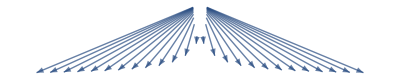
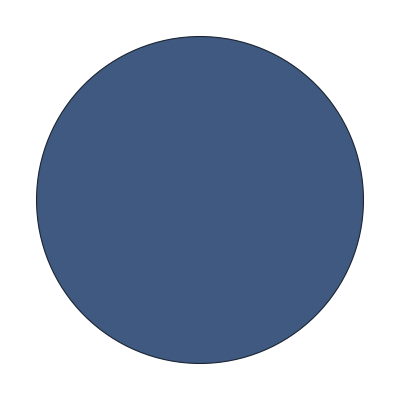
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
XMLTreeView@xmlAssoc
```